Seminarska naloga

Avtor: Matjaž Levstek
Računalniška orodja v matematiki

## LINEARNA FUNKCIJA

Linearna funkcija je funkcija, ki jo lahko zapišemo z enačbo oblike:
f (x) = kx + n,
 kjer sta koeficienta k in n poljubni realni števili.

## GRAF LINEARNE FUNKCIJE

```mathematica
SetOptions[EvaluationNotebook[],Background->LightRed]
```

Graf linearne funkcije je premica:

```mathematica
f[x] = 2x +1
```

1+2 x

```mathematica
Plot[f[x],{x, -3,3}]
```

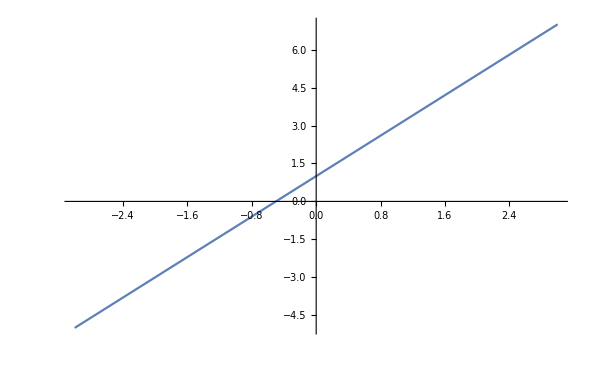

Število N pomeni presečišče grafa z ordinatno osjo. Imenujemo ga začetna vrednost ali odsek na osi y. Število K pa določa smer premice. Imenujemo ga smerni koeficient premice.  Točko ki jo določa k dobimo tako, da se iz točke N pomaknemo za eno enoto v desno in za K enot navzgor (oziroma navzdol, če je k negativen).
Ker dve točki določata premico, lahko graf narišemo tako, da izračunamo koordinate dveh točk ali pa si pomagamo kar s točkama, ki ju določata k in n.

```mathematica
g[x]= 1x +1
```

1+x

```mathematica
h[x]= 1
```

1

```mathematica
e[x] = -1x +1
```

1-x

```mathematica
Plot[{g[x],h[x], e[x]},{x, -1.5, 1.5}, PlotLabels->"Expressions"]
```

```mathematica
Če je k > 0: fukcija narašča,
Če je k = 0: funkcija je konstantna (Graf je vzporeden abscisni osi.),
Če je k < 0: funkcija pada
```

```mathematica
ODNOSI MED PREMICAMI V PROSTORU
```

Dve premici lahko ležita v različnih medsebojnih legah:

1. Premici sta vzporedni, če nimata nobene skupne točke. Taki premici imata enak smerni koeficient(k1= k)-pogoj vzporednosti.

```mathematica
Plot[{3x+ 1, 3x -3},{x,-1.5, 1.5}]
```

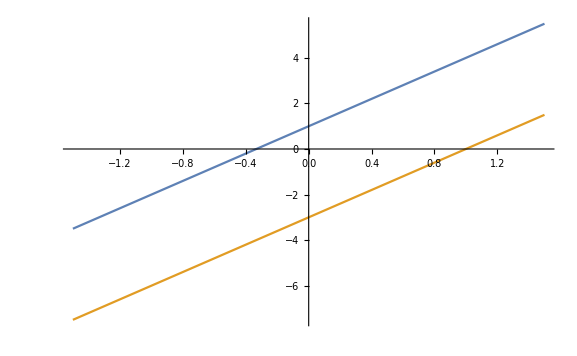

```mathematica
2. Premici, ki se sekata, imata natanko eno skupno točko, ki jo imenujemo presečišče.
```

```mathematica
Plot[{x+2, -2x }, {x, -1, 1}]
```

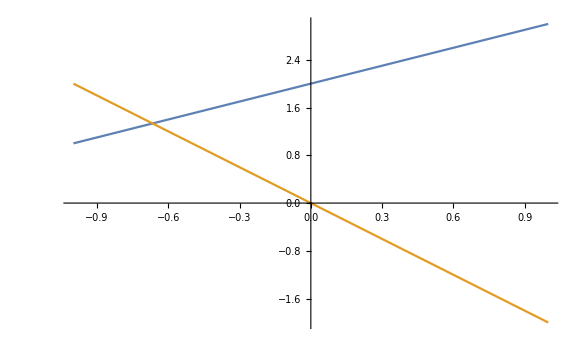

```mathematica
3. Premici, ki se sekata pod pravim kotom sta pravokotni. Smerni koeficient prve premice mora biti obratna in nasprotna vrednost smernega koeficienta druge premice
(k1 = - (1/ k) )-pogoj pravokotnosti.
```

```mathematica
Plot[{x, -x},{x, -2,2}]
```

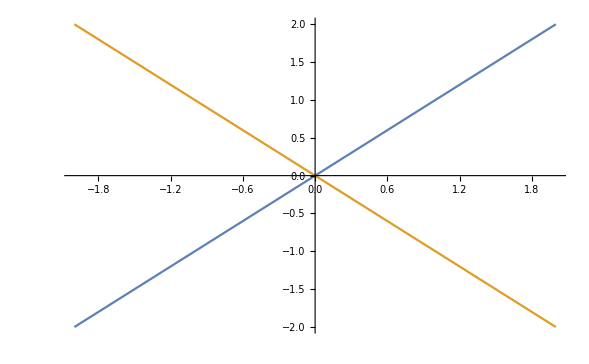

KOT MED PREMICAMA

```mathematica
Kot, ki ga oklepata premica in abscisna os je naklonski kot. Za naklonski kot premice s smernim koeficientom k velja formula:
tg α = k
```

Kot med premicama izračunamo s pomočjo naklonskih kotov dveh premic (φ = |α2 − α1| ), ali pa s pomočjo smernih koeficientov:
tg  φ = |(k1-k)/(1+k1k)|

```mathematica
Plot[{x, -x},{x, -2,2}]
```

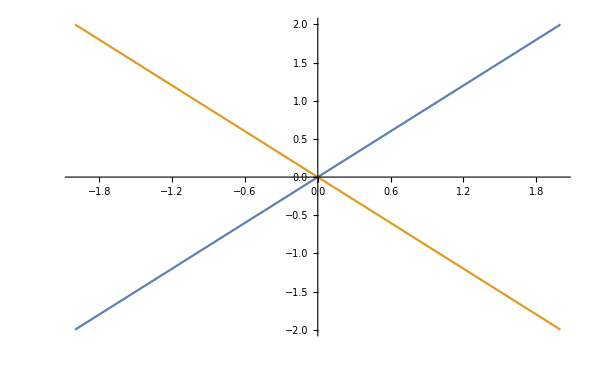

GRAF LINEARNE NEENAČBE